```mathematica
(* toma de datos *)
npr=5; (*num de pasos predictor*)
nc=4;  (*num de pasos corrector*)
ω=4; ϵ=10^(-3);
Y[x_]:={y1[x],y2[x]};
f[x_,Y_]:={{0,1},{-ω^2,0}}.Y + ϵ{0,Y[[1]]^3};
h=0.01;
x0=0;  xf=9;
Y0={1,0};

(*Cálculo coeficientes*)
G[ξ_]:=-ξ/((1-ξ)*Log[1-ξ]);
H[ξ_]:=-ξ/(Log[1-ξ]);
γ=CoefficientList[Normal[Series[G[x],{x,0,npr}]],x];
β=CoefficientList[Normal[Series[H[x],{x,0,nc}]],x];
(*Inicialización*)
sol=NDSolve[{y1'[x]==(f[x,Y[x]])[[1]],y2'[x]==(f[x,Y[x]])[[2]],y1[x0]==Y0[[1]],y2[x0]==Y0[[2]]},{y1,y2},{x,x0,xf}][[1]];
F=Table[f[x0+i*h,(Y[x0+i*h])/.sol],{i,npr,0,-1}];
(*Primer cálculo diferencias divididas*)
For[p=1,p≤npr,p++,
For[i=npr,i≥p,i--,
F[[i+1]]=F[[i]]-F[[i+1]];
];
];
```

```mathematica
(*Método*)
Niter=IntegerPart[(xf-x0)/h];
Y0=Y[x0+npr*h]/.sol;
x0=x0+npr*h;
error={};
For[it=npr+1,it≤Niter,it++,
(*Aproximación predictor + actualización diferencias*)
Yp=Y0+h*(γ.F);
x0=x0+h;

aux=F[[1]];
F[[1]]=f[x0,Yp];
For[i=1,i≤npr,i++,
aux2=F[[i+1]];
F[[i+1]]=F[[i]]-aux;
aux=aux2;
];
(*Aproximación corrector*)
Y0=Y0+h*(β.Take[F,nc+1]);
error=AppendTo[error,{x0,Y0[[1]]-(Y[x0]/.sol)[[1]]}]
]
```

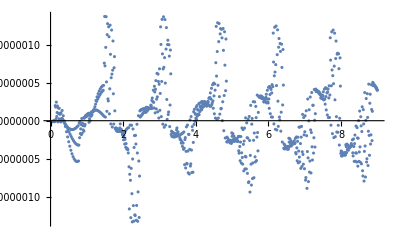

```mathematica
ListPlot[error]
```

```mathematica
MatrixForm[F]
```

(3.96662 | 2.06082
0.0237756 | -0.632839
-0.00630767 | -0.00431083
-0.0000481438 | 0.00100583
0.0000100169 | 8.53547×10^-6
9.33684×10^-8 | -1.60017×10^-6)